{{1/2 (-1+ⅈ √7),1/2 (-1-ⅈ √7)},{{1/4 (-3-ⅈ √7),1},{1/4 (-3+ⅈ √7),1}}}

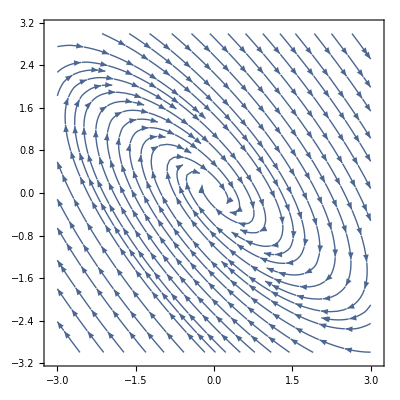

```mathematica
A7 = {{1,2},{-2, -2}};
Eigensystem[A7]
sp7 =StreamPlot[{x+2y,-2x-2y},{x,-3,3},{y,-3,3},Axes -> True]
```

{{1+ⅈ √2,1-ⅈ √2},{{-1-ⅈ √2,1},{-1+ⅈ √2,1}}}

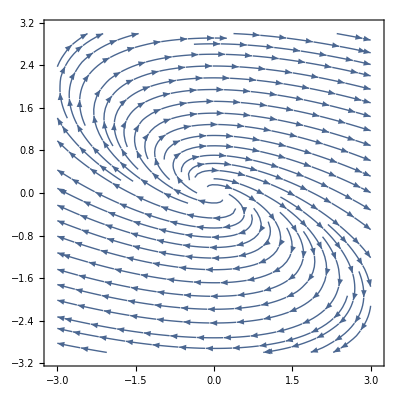

```mathematica
(*The Eigenvalues/EigenVectors are complex so we don't plot them*)

A8 = {{2,3},{-1,0}};
Eigensystem[A8]
sp8= sp7 =StreamPlot[{2x+3y,-x},{x,-3,3},{y,-3,3},Axes -> True]
```

{{1/2 (-3-√17),1/2 (-3+√17)},{{1/2 (5+√17),1},{1/2 (5-√17),1}}}

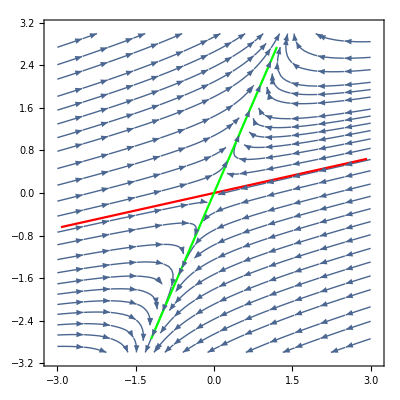

```mathematica
(*The Eigenvalues/EigenVectors are complex so we don't plot them*)

A9 = {{-4,2},{-1,1}};
Eigensystem[A9]
sp9 = StreamPlot[{-4x+2y,-x+y},{x,-3,3},{y,-3,3},Axes -> True];
V9 = Eigenvectors[A9];
Show[StreamPlot[{-4x+2y,-x+y},{x,-3,3},{y,-3,3},Axes -> True], ParametricPlot[{Normalize[V9[[1]]]*t,Normalize[V9[[2]]]*t},{t,-3,3},PlotStyle->{Red, Green}]]
```

```mathematica
(*Note that I just normalize the vecotrs everytime we plot them so the picture comes out nicer*)
```

{{1/2 (-3-√5),1/2 (-3+√5)},{{1/2 (1-√5),1},{1/2 (1+√5),1}}}

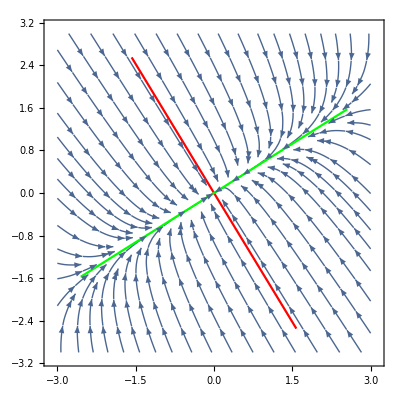

```mathematica
A10={{-1,1},{1,-2}};
Eigensystem[A10]
sp10 = StreamPlot[{-x+y,x-2y},{x,-3,3},{y,-3,3},Axes -> True];
V10 = Eigenvectors[A10];
es10 = ParametricPlot[{Normalize[V10[[1]]]*t,Normalize[V10[[2]]]*t},{t,-3,3},PlotStyle->{Red, Green}];
Show[StreamPlot[{-x+y,x-2y},{x,-3,3},{y,-3,3},Axes -> True], ParametricPlot[{Normalize[V10[[1]]]*t,Normalize[V10[[2]]]*t},{t,-3,3},PlotStyle->{Red, Green}]]
```

{{ⅈ √2,-ⅈ √2},{{-1-ⅈ/(√2),1},{-1+ⅈ/(√2),1}}}

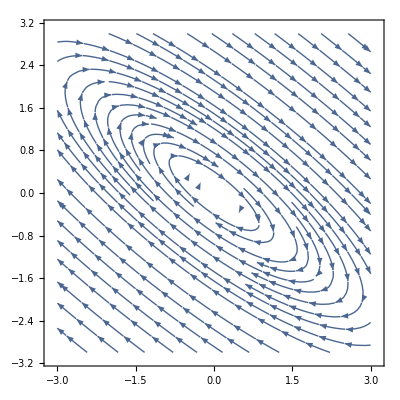

```mathematica
A11 = {{2,3},{-2,-2}};
Eigensystem[A11]
sp11 = StreamPlot[{2x+3y,-2x-2y},{x,-3,3},{y,-3,3},Axes -> True]
```

{{2+√3,2-√3},{{-1+√3,1},{-1-√3,1}}}

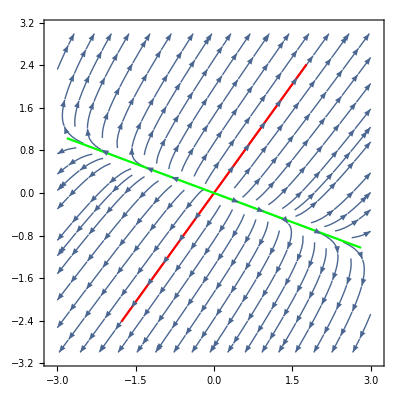

```mathematica
A12 = {{1,2},{1,3}};
Eigensystem[A12]
V12  = Eigenvectors[A12];
Show[StreamPlot[{x+2y,x+3y},{x,-3,3},{y,-3,3},Axes -> True], ParametricPlot[{Normalize[V12[[1]]]*t,Normalize[V12[[2]]]*t},{t,-3,3},PlotStyle->{Red, Green}]]
```